```mathematica
(* Full diamond plots *)
wfAu=5.28;(* Work function for gold *)
zip[a_,b_]:=If[Length[a]≠Length[b],Abort,Table[{a[[i]],b[[i]]},{i,Length[a]}]];
TElines[Vgs_,TEs_]:=Table[Fit[zip[Vgs,TEs[[i]]],{1,vg},vg],{i,Length[TEs]}];
DElines[lines_]:=Table[lines[[i+1]]-lines[[i]],{i,Length[lines]-1}]

GateCoupling[Vgs_,TEs_]:=#[[2]]&/@TElines[Vgs,TEs]/vg
ConductionChannels[vg_,vsd_,defuns_]:=Sum[If[Abs[-wfAu+defuns[[i]][vg,vsd]]≤Abs[vsd/2],1,0],{i,Length[defuns]}];

ConductionChannels0[vg_,vsd_,defuns_]:=Sum[If[Abs[-wfAu+defuns[[i]][vg,0]]≤Abs[vsd/2],1,0],{i,Length[defuns]}];

cfun[x_]:=RGBColor[2.5x,x,0];
DiamondPlot[delines_]:=Module[{xmin,xmax,ymin,ymax},
{{xmin,xmax},{ymin,ymax}}=delines[[1,1]];
ContourPlot[ConductionChannels[g,sd,delines],{g,xmin,xmax},{sd,ymin,ymax},PlotPoints->50,ColorFunction->cfun,FrameLabel->{Subscript[V, g],Subscript[V, sd]}]
]

DiamondPlot0[delines_]:=Module[{xmin,xmax,ymin,ymax},
{{xmin,xmax},{ymin,ymax}}=delines[[1,1]];
ContourPlot[ConductionChannels0[g,sd,delines],{g,xmin,xmax},{sd,ymin,ymax},PlotPoints->50,ColorFunction->cfun,PlotPoints->100,FrameLabel->{Subscript[V, g],Subscript[V, sd]}]
]

GetMoleculeLines[molecule_,dE_,exp_]:=Module[{q,Vgs,Vsds,Vg,Vsd,TE,TEs,Vzero},
q[x_]:=x[[1,1]];
Vg[x_]:=x[[1,2]];
Vsd[x_]:=x[[1,3]];
TE[x_]:=x[[2]];

Get["/home/avery/work/qscf-calculations/SET/results/"<>molecule<>"/"<>dE<>"/"<>exp<>".m"];
Vgs=Union[Vg/@propertylist];
Vsds=Union[Vsd/@propertylist];
TEs=Table[Select[propertylist,q[#]==qq&&Vg[#]==Vgs[[i]]&&Vsd[#]==Vsds[[j]]&][[1,2]],{qq,-2,2},
{i,Length[Vgs]},{j,Length[Vsds]}];

Return[{Vgs,Vsds,TEs}]
];
```

```mathematica
{Vgs,Vsds,TEs}=GetMoleculeLines["OPV5-vnl","0.0005","large-SET"];
```

```mathematica
DEs=Table[TEs[[i+1]]-TEs[[i]],{i,4}];
```

```mathematica
fDEs=Table[Interpolation[Flatten[Table[{{Vgs[[j]],Vsds[[k]]},DEs[[i,j,k]]},{j,Length[Vgs]},{k,Length[Vsds]}],1],InterpolationOrder->{1,1}],{i,4}];
```

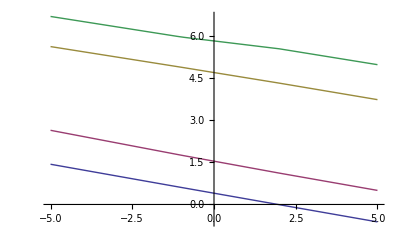

```mathematica
Plot[Evaluate[Table[fDEs[[i]][vg,0],{i,Length[fDEs]}]],{vg,-5,5}]
```

```mathematica
fDEs[[1]]
```

InterpolatingFunction[{{-6.,6.},{-5.,5.}},<>]

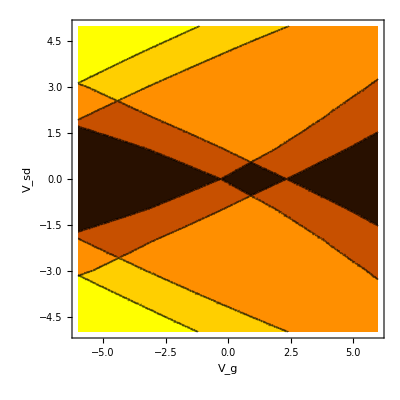
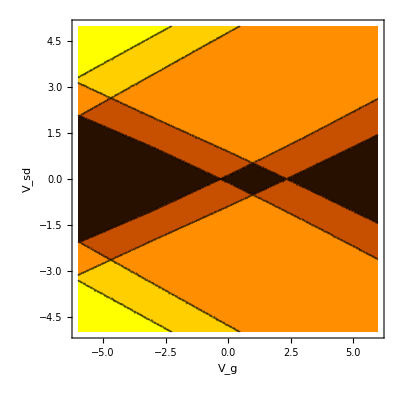

```mathematica
{DiamondPlot[fDEs],
DiamondPlot0[fDEs]}
```

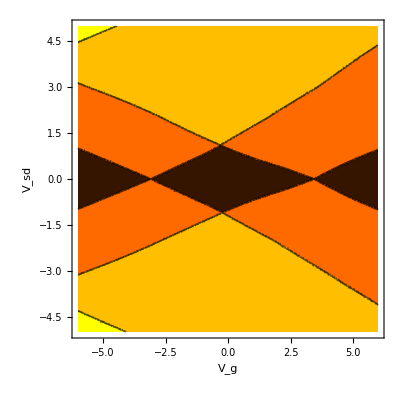
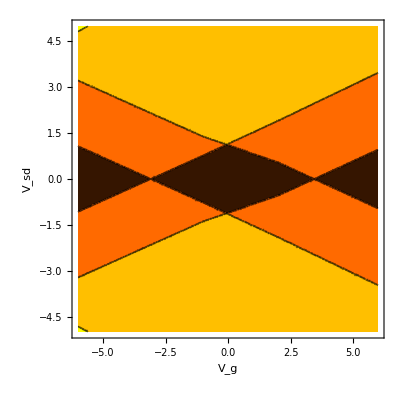

```mathematica
{DiamondPlot[fDEs],
DiamondPlot0[fDEs]}
```

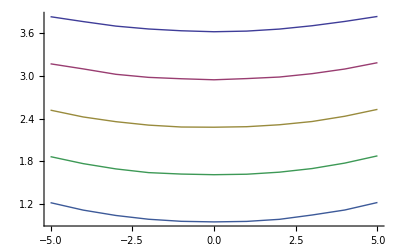

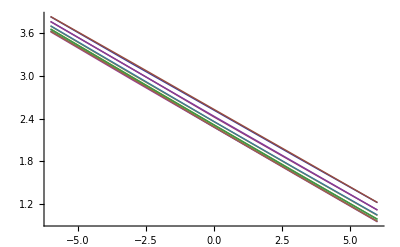

```mathematica
ListPlot[zip[Vsds,#]&/@DEs[[1]],Joined->True]
ListPlot[zip[Vgs,#]&/@Transpose[DEs[[1]]],Joined->True]
```

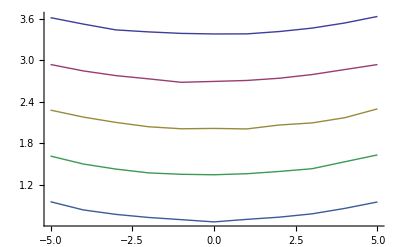

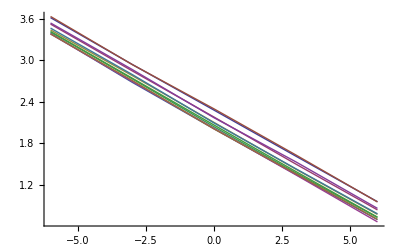

```mathematica
ListPlot[zip[Vsds,#]&/@DEs[[1]],Joined->True]
ListPlot[zip[Vgs,#]&/@Transpose[DEs[[1]]],Joined->True]
```